# Quantum Algorithms: Introduction

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

## Quantum Teleportation

When one has access to both qubits, a SWAP gate for example is enough to send state from one qubit to the other.

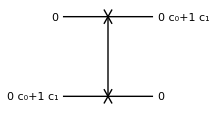

```mathematica
Let[Complex,c]
qc=QuissoCircuit[{LogicalForm[Ket[],S[1]],ProductState[S[2]->{c[0],c[1]}]},SWAP[S[1],S[2]],{LogicalForm[Ket[],S[2]],ProductState[S[1]->{c[0],c[1]}]},"PortSize"->2]
```

```mathematica
out=QuissoFactor@QuissoExpression[qc]
```

(c_0 0_S_1+c_1 1_S_1)⊗0_S_2

### Nonlocality in Entanglement

This is an entangler quantum circuit.

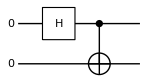

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],CNOT[S[1],S[2]]]
```

```mathematica
vec=QuissoExpression[qc];
vec//LogicalForm
```

(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)

This is a quantum circuit model for the Bel measurement.

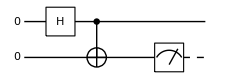

```mathematica
qc2=QuissoCircuit[qc,"Spacer",Measurement@S[2]]
```

This shows that the measurement outcome is just random.

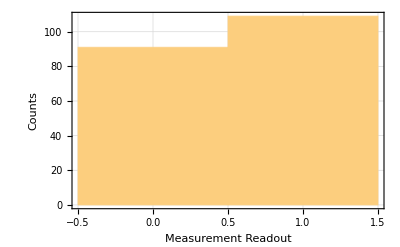

```mathematica
val=Table[out=QuissoExpression[qc2]//Garner;Readout[out,S[2]],{200}];
Histogram[val,FrameLabel->{"Measurement Readout","Counts"},ImageSize->Automatic,FrameStyle->Automatic]
```

Here Alice -- possessing the first qubit -- measures her qubit before Bob measures his qubit.

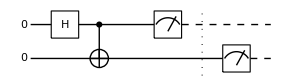

```mathematica
qc3=QuissoCircuit[qc,"Spacer",Measurement@S[1],"Separator",Measurement@S[2]]
```

This illustrates that Bob’s measurement results are affected by Alice measurement.

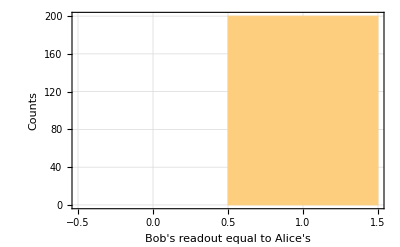

```mathematica
val=Boole@Table[out=QuissoExpression[qc2]//Garner;Equal@@Readout[out,S@{1,2}],{200}];
Histogram[val,{-0.5,1.5,1},FrameLabel->{"Bob's readout equal to Alice's","Counts"},ImageSize->Automatic,FrameStyle->Automatic]
```

### Implementation of Quantum Teleportation

The initial state of the total system at the beginning of the protocol.

```mathematica
Let[Complex,ψ]
vec=Ket[]ψ[0]+Ket[S[3]->1]ψ[1];
vec//LogicalForm
```

0_S_3 ψ_0+1_S_3 ψ_1

```mathematica
tot=BellState[S@{0,2},0]**vec;
tot//LogicalForm
```

(0_S_00_S_20_S_3 ψ_0)/(√2)+(1_S_01_S_20_S_3 ψ_0)/(√2)+(0_S_00_S_21_S_3 ψ_1)/(√2)+(1_S_01_S_21_S_3 ψ_1)/(√2)

The total state is rewritten in the Bell basis for qubits S[2,None] and S[3,None].

```mathematica
bs=BellState[S@{2,3}];
prj=Dyad[#,#]&/@bs;
QuissoFactor/@(prj**tot)//TableForm
```

((0_S_20_S_3+1_S_21_S_3)⊗(0_S_0 ψ_0+1_S_0 ψ_1))/(2 √2)
((0_S_21_S_3+1_S_20_S_3)⊗(1_S_0 ψ_0+0_S_0 ψ_1))/(2 √2)
((-0_S_21_S_3+1_S_20_S_3)⊗(1_S_0 ψ_0-0_S_0 ψ_1))/(2 √2)
((0_S_20_S_3-1_S_21_S_3)⊗(0_S_0 ψ_0-1_S_0 ψ_1))/(2 √2)

Step 1. Alice and Bob generates an entangled pair. Bob prepares a quantum state in a separate qubit.

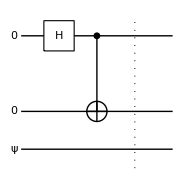

```mathematica
qc1=QuissoCircuit[LogicalForm[Ket[],S@{1,3}],ProductState[S[4]->{ψ[0],ψ[1]},"Label"->Ket[ψ]],S[1,6],CNOT[S[1],S[3]],"Separator","Invisible"->S[2]]
```

Step 2. Bob performs a Bell measurement on his qubits. This can be done by reversing the entangler circuit.

```mathematica
qc2a=QuissoCircuit[CNOT[S[3],S[4]],S[3,6]];
op=QuissoExpression[qc2a];
bs=BellState[S@{3,4}];
ls=op**bs;
LogicalForm@Transpose@Thread[bs->ls]//TableForm
```

(0_S_30_S_4+1_S_31_S_4)/(√2)→0_S_30_S_4
(0_S_31_S_4+1_S_30_S_4)/(√2)→0_S_31_S_4
(0_S_31_S_4-1_S_30_S_4)/(√2)→1_S_31_S_4
(0_S_30_S_4-1_S_31_S_4)/(√2)→1_S_30_S_4

This is the corresponding quantum circuit model.

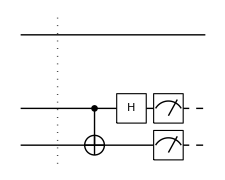

```mathematica
qc2=QuissoCircuit["Separator",qc2a,Measurement@S@{3,4},"Visible"->S[1],"Invisible"->S[2]]
```

Step 3. Bob sends the measurement outcome to Alice through a classical channel.
Step 4. Alice applies a proper Combining these leads to the whole protocol. These steps are simulated by a feedback control.
Combining all these steps comprises, one can transmit a quantum state to a remote party without a quantum channel.

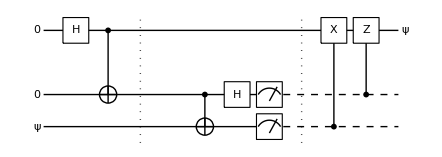

```mathematica
qc=QuissoCircuit[in=ProductState[S[4]->{ψ[0],ψ[1]},"Label"->Ket[ψ]],LogicalForm[Ket[],S@{1,3}],S[1,6],CNOT[S[1],S[3]],"Separator","Spacer",CNOT[S[3],S[4]],S[3,6],
Measurement[S@{3,4}],"Separator",ControlledU[S[4],S[1,1]],ControlledU[S[3],S[1,3]],ProductState[S[1]->{ψ[0],ψ[1]},"Label"->Ket[ψ]],"Invisible"->S[2]]
```

Check the result.

```mathematica
{ψ[0],ψ[1]}=Normalize@Re@RandomVector[];
out=QuissoExpression[qc];
in->LogicalForm@QuissoFactor[out,S@{3,4}]
```

(0.182654 0-0.983177 1)_S_4→0_S_30_S_4⊗(0.182654 0_S_1-0.983177 1_S_1)

## Deutsch-Jozsa Algorithm

### Quantum Oracle

Here is a simple example, which is used in the Deutsch-Jozsa algorithm.

Consider a balanced function f as a classical oracle.

```mathematica
f[0,0]=f[1,1]=0;
f[0,1]=f[1,0]=1;
```

Here is the corresponding quantum oracle.

```mathematica
cc=S@{1,2};
tt=S[3];
qc=QuissoCircuit[Oracle[f,cc,tt]]
```

-Graphics-

```mathematica
op=QuissoExpression[qc]
```

1/2+1/2 S_1^z S_2^z-1/2 S_1^z S_2^z S_3^x+S_3^x/2

```mathematica
bs=Basis@Join[cc,{tt}];
bs//LogicalForm
```

{0_S_10_S_20_S_3,0_S_10_S_21_S_3,0_S_11_S_20_S_3,0_S_11_S_21_S_3,1_S_10_S_20_S_3,1_S_10_S_21_S_3,1_S_11_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
out=op**bs;
out//LogicalForm
```

{0_S_10_S_20_S_3,0_S_10_S_21_S_3,0_S_11_S_21_S_3,0_S_11_S_20_S_3,1_S_10_S_21_S_3,1_S_10_S_20_S_3,1_S_11_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
Thread[bs->out]//LogicalForm//TableForm
```

0_S_10_S_20_S_3→0_S_10_S_20_S_3
0_S_10_S_21_S_3→0_S_10_S_21_S_3
0_S_11_S_20_S_3→0_S_11_S_21_S_3
0_S_11_S_21_S_3→0_S_11_S_20_S_3
1_S_10_S_20_S_3→1_S_10_S_21_S_3
1_S_10_S_21_S_3→1_S_10_S_20_S_3
1_S_11_S_20_S_3→1_S_11_S_20_S_3
1_S_11_S_21_S_3→1_S_11_S_21_S_3

Let us consider another example, which is used in Simon’s algorithm.

Consider a two-to-one function as a classical oracle.

```mathematica
f[0,0]=f[1,1]={0,1};
f[0,1]=f[1,0]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
cc=S@{1,2};
tt=S@{3,4};
qc=QuissoCircuit[Oracle[f,cc,tt]]
```

-Graphics-

```mathematica
op=QuissoOracle[f,cc,tt]
```

1/2 S_3^x S_4^x+1/2 S_1^z S_2^z S_4^x-1/2 S_1^z S_2^z S_3^x S_4^x+S_4^x/2

```mathematica
bs=Basis@Join[cc,tt];
bs//LogicalForm
```

{0_S_10_S_20_S_30_S_4,0_S_10_S_20_S_31_S_4,0_S_10_S_21_S_30_S_4,0_S_10_S_21_S_31_S_4,0_S_11_S_20_S_30_S_4,0_S_11_S_20_S_31_S_4,0_S_11_S_21_S_30_S_4,0_S_11_S_21_S_31_S_4,1_S_10_S_20_S_30_S_4,1_S_10_S_20_S_31_S_4,1_S_10_S_21_S_30_S_4,1_S_10_S_21_S_31_S_4,1_S_11_S_20_S_30_S_4,1_S_11_S_20_S_31_S_4,1_S_11_S_21_S_30_S_4,1_S_11_S_21_S_31_S_4}

```mathematica
out=op**bs;
out//LogicalForm
```

{0_S_10_S_20_S_31_S_4,0_S_10_S_20_S_30_S_4,0_S_10_S_21_S_31_S_4,0_S_10_S_21_S_30_S_4,0_S_11_S_21_S_31_S_4,0_S_11_S_21_S_30_S_4,0_S_11_S_20_S_31_S_4,0_S_11_S_20_S_30_S_4,1_S_10_S_21_S_31_S_4,1_S_10_S_21_S_30_S_4,1_S_10_S_20_S_31_S_4,1_S_10_S_20_S_30_S_4,1_S_11_S_20_S_31_S_4,1_S_11_S_20_S_30_S_4,1_S_11_S_21_S_31_S_4,1_S_11_S_21_S_30_S_4}

```mathematica
Thread[Rule[bs,out]]//LogicalForm//TableForm
```

0_S_10_S_20_S_30_S_4→0_S_10_S_20_S_31_S_4
0_S_10_S_20_S_31_S_4→0_S_10_S_20_S_30_S_4
0_S_10_S_21_S_30_S_4→0_S_10_S_21_S_31_S_4
0_S_10_S_21_S_31_S_4→0_S_10_S_21_S_30_S_4
0_S_11_S_20_S_30_S_4→0_S_11_S_21_S_31_S_4
0_S_11_S_20_S_31_S_4→0_S_11_S_21_S_30_S_4
0_S_11_S_21_S_30_S_4→0_S_11_S_20_S_31_S_4
0_S_11_S_21_S_31_S_4→0_S_11_S_20_S_30_S_4
1_S_10_S_20_S_30_S_4→1_S_10_S_21_S_31_S_4
1_S_10_S_20_S_31_S_4→1_S_10_S_21_S_30_S_4
1_S_10_S_21_S_30_S_4→1_S_10_S_20_S_31_S_4
1_S_10_S_21_S_31_S_4→1_S_10_S_20_S_30_S_4
1_S_11_S_20_S_30_S_4→1_S_11_S_20_S_31_S_4
1_S_11_S_20_S_31_S_4→1_S_11_S_20_S_30_S_4
1_S_11_S_21_S_30_S_4→1_S_11_S_21_S_31_S_4
1_S_11_S_21_S_31_S_4→1_S_11_S_21_S_30_S_4

Solution: This is an interesting twist of the quantum oracle. It is useful in Grover’s search algorithm.

The classical oracle mark the solutions, {0,0}=0 and {1,1}=1 in this particular case.

```mathematica
f[0,0]=1;f[0,1]=0;f[1,0]=0;f[1,1]=1;
```

This quantum circuit model implements the desired mapping.

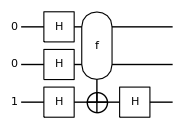

```mathematica
cc={1,2};
tt={3};
ct=Join[cc,tt];
qc=QuissoCircuit[LogicalForm[Ket[S[tt]->1],S[ct]],S[ct,6],Oracle[f,S@cc,S@tt],S[tt,6]]
```

```mathematica
out=QuissoExpression[qc];
QuissoFactor[out,S[tt]]//LogicalForm
```

1_S_3⊗(-1/2 0_S_10_S_2+1/2 0_S_11_S_2+1/2 1_S_10_S_2-1/2 1_S_11_S_2)

Check the result.

```mathematica
bs=Basis[S@cc];
ff=f@@@IntegerDigits[Range[0,2^2-1],2,2];
Thread[bs->Power[-1,ff]]//LogicalForm
```

{0_S_10_S_2→-1,0_S_11_S_2→1,1_S_10_S_2→1,1_S_11_S_2→-1}

```mathematica
new=bs.Power[-1,ff]/2;
new//LogicalForm
```

1/2 (-0_S_10_S_2+0_S_11_S_2+1_S_10_S_2-1_S_11_S_2)

### Deutsch-Jozsa Algorithm

Consider a balanced function as an example.

```mathematica
f[0,0]=f[1,1]=0;
f[0,1]=f[1,0]=1;
```

Here is a quantum circuit model of the Deutsch-Jozsa algorithm. The final Hadamard gate on the third qubit is not necessary, but we put it here to make the output state more readable.

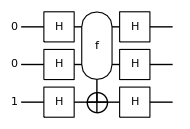

```mathematica
cc={1,2};
tt={3};
all={1,2,3};
qc=QuissoCircuit[LogicalForm[Ket[S[3]->1],S@all],S[all,6],Oracle[f,S@cc,S@tt],S[all,6]]
```

```mathematica
out=QuissoExpression[qc]
```

1_S_11_S_21_S_3

### Bernstein-Vazirani Algorithm

Consider a secrete string of bits. The task is to find the secrete string.

```mathematica
string={0,1};
```

In the Bernstein-Vazirani algorithm, the value out of the classical oracle f is determined by the given secrete string.

```mathematica
f[x__]:=Mod[{x}.string,2]
f[1,1]
```

0

Here is a quantum circuit model of the Bernstein-Vazirani algorithm. The final Hadamard gate on the third qubit is not necessary and we put it here to make the output state more readable.

```mathematica
cc={1,2};
tt={3};
all={1,2,3};
qc=QuissoCircuit[LogicalForm[Ket[S[3]->1],S@all],S[all,6],Oracle[f,S@cc,S@tt],S[all,6]]
```

-Graphics-

```mathematica
out=QuissoExpression[qc]
```

1_S_11_S_21_S_3

Here is the secrete string successfully retrieved.

```mathematica
answer=out[S@cc]
```

{1,1}

### Simon’s Algorithm

Consider again a secrete bit string.

```mathematica
string={1,1};
```

Consider a two-to-one function obeying the rule (specified in Simon’s problem).

```mathematica
f[0,0]=f[1,1]={0,1};
f[0,1]=f[1,0]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

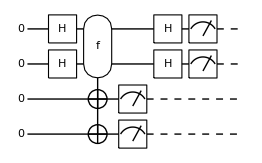

```mathematica
cc={1,2};
tt={3,4};
all=Join[cc,tt];
qc=QuissoCircuit[LogicalForm[Ket[],S@all],S[cc,6],Oracle[f,S@cc,S@tt],Measurement[S@tt],S[cc,6],Measurement[S@cc]]
```

```mathematica
out=QuissoExpression[qc];
LogicalForm[out,S@all]
result=Readout[out,S@cc]
```

-1_S_11_S_21_S_31_S_4

{1,1}

```mathematica
eqs=Table[out=QuissoExpression[Matrix[qc],S@all];result=Readout[out,S@cc],{2}]
```

{{1,1},{1,1}}

## Quantum Fourier Transform

### Definition and Physical Meaning

### Quantum Implementation

We demonstrate it for a four-qubit register.

```mathematica
$N=4;
ss=S[Range[$N],None]
```

{S_1,S_2,S_3,S_4}

Here defined are the controlled-phase gates.

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,k-j],S[k],"Label"->Subscript["R",j-k]]
]/;j>k
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,j-k],S[k],"Label"->Subscript["R",k-j]]
]/;j<k
SW[j_]:=SWAP[S[j],S[$N-j+1]]
```

This is the standard implementation, which can be seen commonly in textbooks.

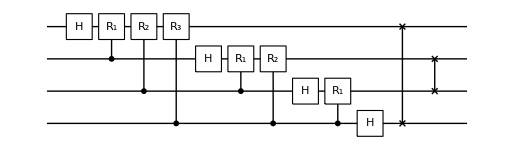

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$N},{j,k,$N}];
qft4a=Join[gates4a,swaps];
qc4a=QuissoCircuit[Sequence@@qft4a]
```

### Semiclassical Implementation

You can convince yourself that the above implementation is equivalent to the following one.

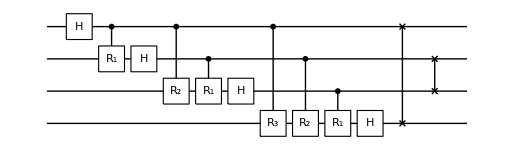

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$N},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuissoCircuit[Sequence@@qft4b]
```

The measurements are explicitly shown.

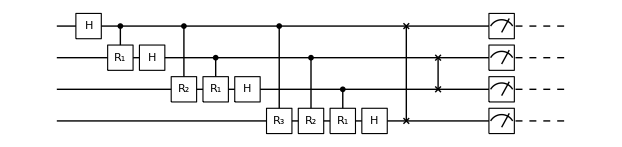

```mathematica
qft4c=Join[gates4b,swaps,{"Spacer",Measurement[ss],"Spacer"}];
qc4c=QuissoCircuit[Sequence@@qft4c]
```

This is the semiclassical implementation.

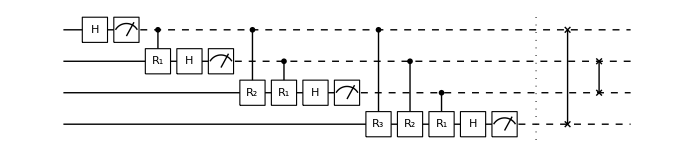

```mathematica
mm=Measurement[ss];
mm=Transpose@{Measurement[ss]};
gates4d=Table[CP[j,k],{k,1,$N},{j,1,k}];
more=Catenate[Join@@@Thread[{gates4d,mm}]];
qft4d=Join[more,{"Separator"},swaps];
qc4d=QuissoCircuit[Sequence@@qft4d]
```

Check the equivalence.

```mathematica
mat4a=Matrix[qc4a];
mat4b=Matrix[qc4b];
mat4a-mat4b//Simplify//Norm
```

0

## Quantum Phase Estimation

### Definition

### Implementation

We take an ancillary register consisting of three qubits.

```mathematica
m=4;
ancilla=Range[m];
sys=m+1;
```

We consider a rotation around the z-axis for the unitary operator. In this case, the logical basis consists of the eigenstates of the unitary operator.

```mathematica
p=18/25;
U=Rotation[p 2Pi,S[sys,3]];
```

Here is the controlled-U^(2^(m-j)) operator to be used in the phase estimation algorithm.

```mathematica
ctrlU[j_]:=ControlledU[S[j],MultiplyPower[U,Power[2,m-j]],"Label"->Superscript["U",Superscript["2",ToString[m-j]]],
"LabelSize"->0.65]
```

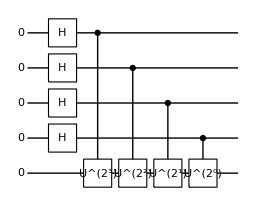

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@ancilla],LogicalForm[Ket[],S@sys],{S[ancilla,6],"LabelSize"->0.8},ctrlU[1],ctrlU[2],ctrlU[3],ctrlU[4]]
```

As the QFT step is clear, we do not simulate the step here and just process the data using the built-in function Fourier.

```mathematica
vec=QuissoExpression[qc];
out=Fourier@Matrix[vec,S@ancilla]
```

{0.0146117-0.0449701 ⅈ,0.00625173-0.0528206 ⅈ,-0.00498774-0.0633752 ⅈ,-0.0225159-0.0798352 ⅈ,-0.0573411-0.112538 ⅈ,-0.17816-0.225994 ⅈ,0.690635+0.589858 ⅈ,0.154844+0.0867168 ⅈ,0.0955664+0.0310514 ⅈ,0.0715134+0.00846417 ⅈ,0.057667-0.00453849 ⅈ,0.0480647-0.0135556 ⅈ,0.0405163-0.0206441 ⅈ,0.0339768-0.0267851 ⅈ,0.027817-0.0325695 ⅈ,0.0215406-0.0384635 ⅈ}

```mathematica
Prob=Abs[out]^2
```

{0.00223581,0.0028291,0.00404129,0.00688062,0.0159529,0.0828144,0.824909,0.0314965,0.0100971,0.00518581,0.00334608,0.00249397,0.00206775,0.00187186,0.00183456,0.00194343}

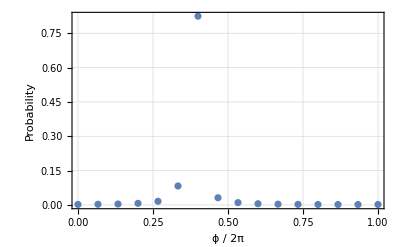

```mathematica
ListPlot[Prob,PlotRange->All,DataRange->{0,1},FrameLabel->{"ϕ / 2π","Probability"},FrameStyle->Automatic,ImageSize->Automatic]
```